```mathematica
data=Table[ -2x+3 +RandomReal[{-10,10}],{x,0,20,0.25}];
```

```mathematica
Dynamic@ListPlot[Transpose@{Table[x,{x,0,20,0.25}],data}]
```

```mathematica
X=Table[x,{x,0,20,0.25}];
```

```mathematica
XX=Transpose@{Table[x,{x,0,20,0.25}],data};
```

```mathematica
A:=Table[{1,x},{x,0,20,0.25}];
```

```mathematica
A2:=Table[{1,x,x^2},{x,0,20,0.25}];
```

```mathematica
A3:=Table[{1,x,x^2,x^3},{x,0,20,0.25}];
```

```mathematica
Ap:=Inverse[Transpose[A].A].Transpose[A];
```

```mathematica
Th:=Ap.data
```

```mathematica
Dynamic@Th
```

```mathematica
L:=Sum[(data[[i]]-(A.Th)[[i]])^2,{i,1,Length[data]}]
```

```mathematica
Dynamic@L
```

```mathematica
A.Th
```

{-17.7617,-16.0466,-14.7417,-13.8468,-13.3621,-13.2876,-13.6231,-14.3688,-15.5246,-17.0905,-19.0666,-21.4528,-24.2491,-27.4555,-31.0721,-35.0988,-39.5356,-44.3826,-49.6396,-55.3068,-61.3842,-67.8716,-74.7692,-82.0769,-89.7948,-97.9227,-106.461,-115.409,-124.767,-134.536,-144.714,-155.303,-166.302,-177.711,-189.53,-201.759,-214.399,-227.448,-240.908,-254.778,-269.058,-283.748,-298.848,-314.358,-330.278,-346.609,-363.349,-380.5,-398.061,-416.032,-434.413,-453.205,-472.406,-492.017,-512.039,-532.471,-553.313,-574.565,-596.227,-618.299,-640.782,-663.674,-686.977,-710.69,-734.813,-759.346,-784.289,-809.642,-835.406,-861.579,-888.163,-915.157,-942.561,-970.375,-998.599,-1027.23,-1056.28,-1085.73,-1115.6,-1145.87,-1176.56}

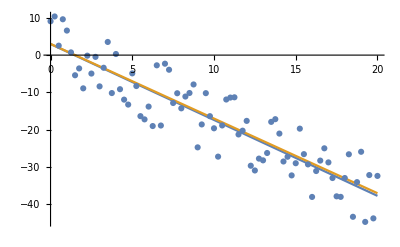

```mathematica
Show[Plot[{Th[[2]]x+Th[[1]],-2x+3 },{x,0,20},PlotRange->All],ListPlot[XX]]
```

```mathematica
Yk:=A.Th;
```

```mathematica
Sum[(data-Th.Transpose[A])[[i]],{i,1,Length[data]}]
```

3.55271×10^-14

```mathematica
der2:=2Sum[(data[[i]]-Yk[[i]])X[[i]],{i,1,Length[data]}]
```

```mathematica
(data-Yk).X
```

-6.46618×10^8

```mathematica
Th[[2]]=Th[[2]]-10^-4*der2
```

3850.97